## 133La

```mathematica
ClearAll["Global`*"]
```

```mathematica
yrastEn=Sort[{7255,6145,5199,4227.0,3293.0,2450.0,1661.0,980.0,535.0}];
wob1En=Sort[{4325.0,3432.0,2535.0,1738.0,1153.0}];
yrastSpin=Table[i/2,{i,11,43,4}];
wob1Spin=Table[i/2,{i,13,29,4}];
```

```mathematica
omega[data_]:=Table[1/2(data[[i]]-data[[i-1]])/1000,{i,2,Length[data]}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2000(yrast[[i]]+yrast[[i+1]])},{i,1,Length[b1]}];
```

```mathematica
omegaYrast=omega[yrastEn];
omegawob1=omega[wob1En];
```

```mathematica
fig=ListPlot[{Table[{omegaYrast[[i]],yrastSpin[[i+1]]},{i,1,Length[omegaYrast]}],Table[{omegawob1[[i]],wob1Spin[[i+1]]},{i,1,Length[omegawob1]}]},Joined->True,PlotMarkers->{Automatic, Medium},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"ω_rot [MeV]","I [ℏ]"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},PlotRange->Full,ImageSize->350,FrameTicks->{{Automatic,None},{{0.2,0.3,0.4,0.5},None}},Epilog->{Style[Line[{{-100,5.5},{100,5.5}}],Thick,Magenta,DotDashed,Opacity[1]],Inset[Style[Framed[Row[{Superscript["","133"],"La"}]],FontFamily->"Times",Black,18,Bold],Scaled[{0.25,0.12}]]},PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}},PlotLegends->Placed[{"yrast","wobb"},{0.25,0.8}]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/133La.pdf",fig];
```

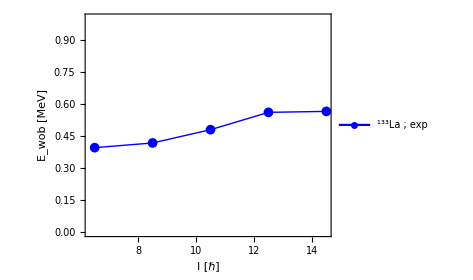

```mathematica
data=wobbling[yrastEn,wob1En,wob1Spin];
fig2=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","133"],"La ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/133La_wob.pdf",fig2];
Show[fig2]
```